```mathematica
{P[0],P[1],P[2]}==Table[Sum[d[i,j,k] σ[j,k],{j,0,2},{k,0,2}],{i,0,2}]
```

{P[0],P[1],P[2]}=={d[0,0,0] σ[0,0]+d[0,0,1] σ[0,1]+d[0,0,2] σ[0,2]+d[0,1,0] σ[1,0]+d[0,1,1] σ[1,1]+d[0,1,2] σ[1,2]+d[0,2,0] σ[2,0]+d[0,2,1] σ[2,1]+d[0,2,2] σ[2,2],d[1,0,0] σ[0,0]+d[1,0,1] σ[0,1]+d[1,0,2] σ[0,2]+d[1,1,0] σ[1,0]+d[1,1,1] σ[1,1]+d[1,1,2] σ[1,2]+d[1,2,0] σ[2,0]+d[1,2,1] σ[2,1]+d[1,2,2] σ[2,2],d[2,0,0] σ[0,0]+d[2,0,1] σ[0,1]+d[2,0,2] σ[0,2]+d[2,1,0] σ[1,0]+d[2,1,1] σ[1,1]+d[2,1,2] σ[1,2]+d[2,2,0] σ[2,0]+d[2,2,1] σ[2,1]+d[2,2,2] σ[2,2]}

```mathematica
FullSimplify[{P[0],P[1],P[2]}=={d[0,0,0] σ[0,0]+d[0,0,1] σ[0,1]+d[0,0,2] σ[0,2]+d[0,1,0] σ[1,0]+d[0,1,1] σ[1,1]+d[0,1,2] σ[1,2]+d[0,2,0] σ[2,0]+d[0,2,1] σ[2,1]+d[0,2,2] σ[2,2],d[1,0,0] σ[0,0]+d[1,0,1] σ[0,1]+d[1,0,2] σ[0,2]+d[1,1,0] σ[1,0]+d[1,1,1] σ[1,1]+d[1,1,2] σ[1,2]+d[1,2,0] σ[2,0]+d[1,2,1] σ[2,1]+d[1,2,2] σ[2,2],d[2,0,0] σ[0,0]+d[2,0,1] σ[0,1]+d[2,0,2] σ[0,2]+d[2,1,0] σ[1,0]+d[2,1,1] σ[1,1]+d[2,1,2] σ[1,2]+d[2,2,0] σ[2,0]+d[2,2,1] σ[2,1]+d[2,2,2] σ[2,2]}/.{d[0,0,0]->d000,d[0,0,1]->d001,d[0,0,2]->d002,
d[0,1,0]->d010,d[0,1,1]->d011,d[0,1,2]->d012,
d[0,2,0]->d020,d[0,2,1]->d021,d[0,2,2]->d022,
d[1,0,0]->d100,d[1,0,1]->d101,d[1,0,2]->d102,
d[1,1,0]->d110,d[1,1,1]->d111,d[1,1,2]->d112,
d[1,2,0]->d120,d[1,2,1]->d121,d[1,2,2]->d122,
d[2,0,0]->d200,d[2,0,1]->d201,d[2,0,2]->d202,
d[2,1,0]->d210,d[2,1,1]->d211,d[2,1,2]->d212,
d[2,2,0]->d220,d[2,2,1]->d221,d[2,2,2]->d222,
σ[1,0]->σ01,σ[0,1]->σ01,σ[0,2]->σ02,σ[2,0]->σ02}]
```

{P[0],P[1],P[2]}=={(d001+d010) σ01+(d002+d020) σ02+d000 σ[0,0]+d011 σ[1,1]+d012 σ[1,2]+d021 σ[2,1]+d022 σ[2,2],(d101+d110) σ01+(d102+d120) σ02+d100 σ[0,0]+d111 σ[1,1]+d112 σ[1,2]+d121 σ[2,1]+d122 σ[2,2],(d201+d210) σ01+(d202+d220) σ02+d200 σ[0,0]+d211 σ[1,1]+d212 σ[1,2]+d221 σ[2,1]+d222 σ[2,2]}

```mathematica
Length[{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}]
```

36

```mathematica
Table[3+1.25k,{k,0,22}]
```

{3.,4.25,5.5,6.75,8.,9.25,10.5,11.75,13.,14.25,15.5,16.75,18.,19.25,20.5,21.75,23.,24.25,25.5,26.75,28.,29.25,30.5}

```mathematica
Solve[3/60.==30.5/x,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→610.}}

```mathematica
Table[60+7k,{k,0,22}]
```

{60,67,74,81,88,95,102,109,116,123,130,137,144,151,158,165,172,179,186,193,200,207,214}

```mathematica
Solve[60+25 q==300.0,q]
```

{{q→9.6}}

```mathematica
Table[7+0.7k,{k,0,22}]
```

{7.,7.7,8.4,9.1,9.8,10.5,11.2,11.9,12.6,13.3,14.,14.7,15.4,16.1,16.8,17.5,18.2,18.9,19.6,20.3,21.,21.7,22.4}

```mathematica
Solve[5+22 g==20.,g]
```

{{g→0.681818}}

```mathematica
300*0.58
```

174.

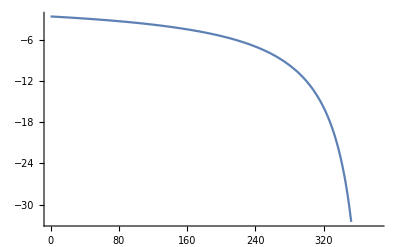

```mathematica
Plot[1000/(T0-383),{T0,0,383}]
```

```mathematica
B = 186;
```

```mathematica
172.74 == λ + (2/3)*109.62
```

172.74==73.08+λ

```mathematica
({{172.74+(4/3)109.62, 172.74-(2/3)109.62, 172.74-(2/3)109.62, 0, 0, 0}, {172.74-(2/3)109.62, 172.74+(4/3)109.62, 172.74-(2/3)109.62, 0, 0, 0}, {172.74-(2/3)109.62, 172.74-(2/3)109.62, 172.74+(4/3)109.62, 0, 0, 0}, {0, 0, 0, 109.62, 0, 0}, {0, 0, 0, 0, 109.62, 0}, {0, 0, 0, 0, 0, 109.62}})//MatrixForm
```

(318.9 | 99.66 | 99.66 | 0 | 0 | 0
99.66 | 318.9 | 99.66 | 0 | 0 | 0
99.66 | 99.66 | 318.9 | 0 | 0 | 0
0 | 0 | 0 | 109.62 | 0 | 0
0 | 0 | 0 | 0 | 109.62 | 0
0 | 0 | 0 | 0 | 0 | 109.62)

```mathematica
G12(P11 P22+P22 P33 + P11 P33)
```

```mathematica
G44((P12+P21)^2+(P23+P32)^2+(P31+P13)^2)
```

G44 ((P12+P21)^2+(P13+P31)^2+(P23+P32)^2)

```mathematica
FullSimplify[Expand[G44/2 ((P12+P21)^2+(P13+P31)^2+(P23+P32)^2)]]
```

1/2 G44 ((P12+P21)^2+(P13+P31)^2+(P23+P32)^2)